```mathematica
<< "C:\\Documents and Settings\\ocroissant\\My Documents\\BiHeston\\BiHeston_Process.m"
```

```mathematica
<< "C:\\Documents and Settings\\ocroissant\\My Documents\\BiHeston\\BiHeston_VanillaInstruments.m"
```

## Calibration of the underlyings

```mathematica
InitializeMarketData[]:=Module[{},cms2Tab=Table[CMSData[[i,j]],{i,3,202},{j,1,10}];
cms5Tab=Table[CMSData[[i,j]],{i,3,202},{j,12,21}];
cms10Tab=Table[CMSData[[i,j]],{i,3,202},{j,23,32}];
cms20Tab=Table[CMSData[[i,j]],{i,3,202},{j,34,43}];
cms30Tab=Table[CMSData[[i,j]],{i,3,202},{j,45,54}];
NormalVol2Y10YTab=Table[CMSData[[i,j]],{i,215,261},{j,44,55}];
NormalVol2Y20YTab=Table[CMSData[[i,j]],{i,274,320},{j,44,55}];
NormalVol2Y30YTab=Table[CMSData[[i,j]],{i,333,379},{j,44,55}];
NormalVol5Y10YTab=Table[CMSData[[i,j]],{i,392,438},{j,44,55}];
NormalVol5Y20YTab=Table[CMSData[[i,j]],{i,451,497},{j,44,55}];
NormalVol5Y30YTab=Table[CMSData[[i,j]],{i,510,556},{j,44,55}];
spreadoptionMaturitiesTab=Table[CMSData[[i,1]],{i,215,261}];
]
```

```mathematica
CMSData=Import["C:\\Documents and Settings\\ocroissant\\My Documents\\CMS_Spread_Market.csv"];
InitializeMarketData[];Length[CMSData]
```

556

```mathematica
MarketCMSForward[5,"cms5"]
```

{0.0481839,0.047903,0.04819}

```mathematica
MarketCMSOptionVol[0.1,5,"cms5"]
```

{0.135659,0.137155,0.135627}

```mathematica
MarketCMSSpreadOptionNormalVol[0.01,5,"cms2","cms10"]
```

{0.00284041,0.00289,0.00284}

```mathematica
NormalVol2Y10YTab[[1]]
```

{0.00346,0.00321,0.00293,0.00265,0.00237,0.00219,0.00231,0.0026,0.00289,0.0034,0.0022,0.00237}

```mathematica
MarketCMSSpreadOptionNormalVol[K_,T_,tenor1_,tenor2_]:=
Module[{tab,opt1,opt2,i,j,
StrikeList={-0.01,-0.0075,-0.005,-0.0025,0,0.0025,0.005,0.0075,0.01,0.015},
smile1,smile2,inter1,inter2
},tab=Switch[tenor1,
"cms2",Switch[tenor2,"cms10",NormalVol2Y10YTab,"cms20",NormalVol2Y20YTab,"cms30",NormalVol2Y30YTab],
"cms5",Switch[tenor2,"cms10",NormalVol5Y10YTab,"cms20",NormalVol5Y20YTab,"cms30",NormalVol5Y30YTab]
];
(* determination du rang de la maturité *)
i=2;
While[(i<Length[spreadoptionMaturitiesTab])&&( T>spreadoptionMaturitiesTab[[i]]),i++];
(*interpolation *)
smile1=Table[{StrikeList[[j]],tab[[i-1,j]]},{j,1,Length[StrikeList]}];
smile2=Table[{StrikeList[[j]],tab[[i,j]]},{j,1,Length[StrikeList]}];
inter1=Interpolation[smile1];
inter2=Interpolation[smile2];
opt1=inter1[K];
opt2=inter2[K];
{opt1+(T-spreadoptionMaturitiesTab[[i-1]])/(spreadoptionMaturitiesTab[[i]]-spreadoptionMaturitiesTab[[i-1]])(opt2-opt1),opt1,opt2}
]
```

```mathematica
MarketCMSOptionVol[K_,T_,tenor_]:=
Module[{tab,opt1,opt2,i},
tab=Switch[tenor,"cms2",cms2Tab,"cms5",cms5Tab,"cms10",cms10Tab,"cms20",cms20Tab,"cms30",cms30Tab];
(* determination du rang de la maturité *)
i=2;
While[(i<Length[tab])&&( T>tab[[i,1]]),i++];
(*interpolation *)
opt1=SABROptionDirect2[tab[[i-1,2]],tab[[i-1,3]],tab[[i-1,4]],tab[[i-1,5]],tab[[i-1,6]],K,tab[[i-1,1]]][[1]];
opt2=SABROptionDirect2[tab[[i,2]],tab[[i,3]],tab[[i,4]],tab[[i,5]],tab[[i,6]],K,tab[[i,1]]][[1]];
{opt1+(T-tab[[i-1,1]])/(tab[[i,1]]-tab[[i-1,1]])(opt2-opt1),opt1,opt2}
]
```

```mathematica
MarketCMSForward[T_,tenor_]:=
Module[{tab,opt1,opt2},tab=Switch[tenor,"cms2",cms2Tab,"cms5",cms5Tab,"cms10",cms10Tab,"cms20",cms20Tab,"cms30",cms30Tab];
(* determination du rang de la maturité *)
i=2;
While[(i<Length[tab])&&( T>tab[[i,1]]),i++];
opt1=tab[[i-1,2]];
opt2=tab[[i,2]];
{opt1+(T-tab[[i-1,1]])/(tab[[i,1]]-tab[[i-1,1]])(opt2-opt1),opt1,opt2}
]
```

## Calibration

Nb1=30 Nb1n=8 Nb2=20

S=(0.0481839
0.0481839) Σ=(0.01 | 0.
0. | 0.01)M=(-0.35 | 0.
0. | -0.35) Σinf=(0.04 | 0.
0. | 0.03) Q=(0.25 | 0
0 | 0.25) ρ=(-0.45
-0.45) Imaginary Shifts=(2
2) βm =(0.224 | 0.
0. | 0.168)

{NbLegCoef1,NbLegCoef1n,period1,period1n,ϵ1,imax}={30,8,1,3,1.×10^-7,60}{NbLegCoef2,period2,period2n,ϵ2}={20,1,2,1.×10^-8}

BiHestonLaplaceQuickTransform2[M,Q,ρ, μ,Σ,{-ⅈ 1,-ⅈ 1},βm,τ]=0.886446+0.068277 ⅈ

integrand(0.1,0.1)={142.512,114.099,95.1077,81.5182,71.3127,67.9084,64.8125,61.9849,59.3923,58.1751,57.0064,55.8835,54.8037,53.7645,52.7637,50.8691,49.1049,47.458,45.9173,44.4727,43.1155,41.838,40.6335,39.4958,38.4195,37.3999,36.4325,35.5135,31.5308,29.5396,28.3449,25.7386,24.3907,23.5671,22.7968,21.7303,20.1563,18.7927,17.6,16.548,15.6133,14.7773,14.0252,12.727,11.646}

{λH2,θH2,νH2,ρH2}={0.7,0.03,0.5,-0.45}

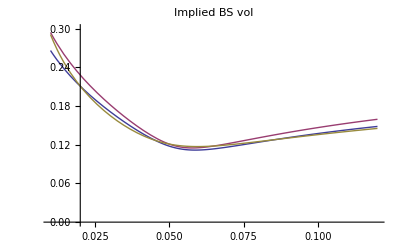
{36.083,-Graphics-}

```mathematica
Timing[Module[{S1,S2,M1=-0.35,M2=-0.35,ρs=0.,ρsinf=0.,ρm1=0.,ρm2=0.,ρ1=-0.45,ρ2=-0.45, Σ1,Σ2,θ1,θ2,τ=5,α1=1,a=1,M,Σinf,Σ,Q,βm,S,ρ,printflag={1},μ={0,0},inter1,inter2,inter3,smileLN,interLN,prices,tenor="cms5",K,β,limsup=1000,νH2,ρH2,λH2,θH2},
Σ1=0.01;Σ2=0.01;θ1=4.Σ1;θ2=3.Σ2;
S1=MarketCMSForward[τ,tenor][[1]];S2=S1;
M=({{M1, ρm1 √(M1 M2)}, {ρm2 √(M1 M2), M2}});Σinf=({{θ1, √(θ1 θ2) ρsinf}, {√(θ1 θ2) ρsinf, θ2}});Σ=({{Σ1, √(Σ1 Σ2) ρs}, {√(Σ1 Σ2) ρs, Σ2}});S={S1,S2};ρ={ρ1,ρ2};
strikes={0.01,0.0125,0.015,0.0175,0.02,0.021,0.022,0.023,0.024,0.0245,0.025,0.0255,0.026,0.0265,0.027,0.028,0.029,0.03,0.031,0.032,0.033,0.034,0.035,0.036,0.037,0.038,0.039,0.04,0.045,0.048,0.05,0.055,0.058,0.06,0.062,0.065,0.07,0.075,0.08,0.085,0.09,0.095,0.1,0.11,0.12};
Q=({{0.25, 0}, {0, 0.25}});
prices=SmileBiHestonUnderlying2Vanilla2[S,α1,a,strikes,τ,Σ,M,Σinf,Q,ρ,μ,printflag];
smile=Table[{strikes[[i]],ImpVolBS[S1,strikes[[i]],τ,prices[[i]]]},{i,1,Length[strikes]}];
inter=Interpolation[smile];
νH2=2 √(Q[[1,2]]^2+Q[[2,2]]^2);
ρH2=ρ2;
λH2=-2M[[2,2]];
θH2=θ2+(√(θ1 θ2) ρsinf-√(Σ1 Σ2) ρs)M[[1,2]]/M[[2,2]];
Print["{λH2,θH2,νH2,ρH2}=",{λH2,θH2,νH2,ρH2}];
prices=Table[LNHestonVanillaCall[S2,strikes[[i]],Σ2,τ,λH2,θH2,νH2,ρH2,limsup],{i,1,Length[strikes]}];
smile=Table[{strikes[[i]],ImpVolBS[S1,strikes[[i]],τ,prices[[i]]]},{i,1,Length[strikes]}];
inter2=Interpolation[smile];
smileMarket=Table[{strikes[[i]],MarketCMSOptionVol[strikes[[i]],τ,tenor][[1]]},{i,1,Length[strikes]}];
interMarket=Interpolation[smileMarket];
Plot[{inter[x],inter2[x],interMarket[x]},{x,strikes[[1]],Last[strikes]},PlotLabel->"Implied BS vol",
PlotLegend->{"BiHestonUnderlying2","Heston","Market"},LegendPosition->{1,0},PlotRange->{0,0.3}]]]
```

Nb1=30 Nb1n=10 Nb2=30

S=(0.0481839
0.0481839) Σ=(0.01 | 0.
0. | 0.01)M=(-0.35 | 0.
0. | -0.35) Σinf=(0.03 | 0.
0. | 0.03) Q=(0.25 | 0
0 | 0.25) ρ=(-0.45
-0.45) Imaginary Shifts=(2
1.1) βm =(0.168 | 0.
0. | 0.168)

{NbLegCoef1,NbLegCoef1n,period1,period1n,ϵ1,imax}={30,10,12,5,1.×10^-7,10}{NbLegCoef2,period2,period2n,ϵ2}={30,12,1.6,1.×10^-7}

BiHestonLaplaceQuickTransform2[M,Q,ρ, μ,Σ,{-ⅈ 1,-ⅈ 1},βm,τ]=0.899073+0.0610405 ⅈ

integrand(0.1,0.1)={7.49706,5.99938,4.99882,4.28311,3.74579,3.56659,3.40364,3.25483,3.1184,3.05435,2.99286,2.93378,2.87696,2.82229,2.76964,2.66998,2.57718,2.49056,2.40953,2.33356,2.26219,2.19502,2.13168,2.07187,2.01529,1.96169,1.91084,1.86253,1.65322,1.54859,1.48583,1.34892,1.27813,1.23488,1.19442,1.13842,1.05579,0.984209,0.921609,0.866403,0.817357,0.773497,0.734045,0.665953,0.60927}

{λH2,θH2,νH2,ρH2}={0.7,0.03,0.5,-0.45}

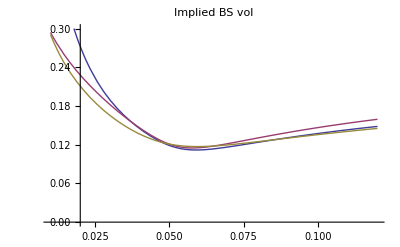
{6.567,-Graphics-}

```mathematica
Timing[Module[{S1,S2,M1=-0.35,M2=-0.35,ρs=0.,ρsinf=0.,ρm1=0.,ρm2=0.,ρ1=-0.45,ρ2=-0.45, Σ1,Σ2,θ1,θ2,τ=5,α1=1,a=1,M,Σinf,Σ,Q,βm,S,ρ,printflag={1},μ={0,0},inter1,inter2,inter3,smileLN,interLN,prices,tenor="cms5",K,β,limsup=1000,νH2,ρH2,λH2,θH2},
Σ1=0.01;Σ2=0.01;θ1=3.Σ1;θ2=3.Σ2;
S1=MarketCMSForward[τ,tenor][[1]];S2=S1;
M=({{M1, ρm1 √(M1 M2)}, {ρm2 √(M1 M2), M2}});Σinf=({{θ1, √(θ1 θ2) ρsinf}, {√(θ1 θ2) ρsinf, θ2}});Σ=({{Σ1, √(Σ1 Σ2) ρs}, {√(Σ1 Σ2) ρs, Σ2}});S={S1,S2};ρ={ρ1,ρ2};
strikes={0.01,0.0125,0.015,0.0175,0.02,0.021,0.022,0.023,0.024,0.0245,0.025,0.0255,0.026,0.0265,0.027,0.028,0.029,0.03,0.031,0.032,0.033,0.034,0.035,0.036,0.037,0.038,0.039,0.04,0.045,0.048,0.05,0.055,0.058,0.06,0.062,0.065,0.07,0.075,0.08,0.085,0.09,0.095,0.1,0.11,0.12};
Q=({{0.25, 0}, {0, 0.25}});
prices=SmileBiHestonUnderlying1Vanilla2[S,α1,a,strikes,τ,Σ,M,Σinf,Q,ρ,μ,printflag];
smile=Table[{strikes[[i]],ImpVolBS[S1,strikes[[i]],τ,prices[[i]]]},{i,1,Length[strikes]}];
inter=Interpolation[smile];
νH2=2 √(Q[[1,2]]^2+Q[[2,2]]^2);
ρH2=ρ2;
λH2=-2M[[2,2]];
θH2=θ2+(√(θ1 θ2) ρsinf-√(Σ1 Σ2) ρs)M[[1,2]]/M[[2,2]];
Print["{λH2,θH2,νH2,ρH2}=",{λH2,θH2,νH2,ρH2}];
prices=Table[LNHestonVanillaCall[S2,strikes[[i]],Σ2,τ,λH2,θH2,νH2,ρH2,limsup],{i,1,Length[strikes]}];
smile=Table[{strikes[[i]],ImpVolBS[S1,strikes[[i]],τ,prices[[i]]]},{i,1,Length[strikes]}];
inter2=Interpolation[smile];
smileMarket=Table[{strikes[[i]],MarketCMSOptionVol[strikes[[i]],τ,tenor][[1]]},{i,1,Length[strikes]}];
interMarket=Interpolation[smileMarket];
Plot[{inter[x],inter2[x],interMarket[x]},{x,strikes[[1]],Last[strikes]},PlotLabel->"Implied BS vol",
PlotLegend->{"BiHestonUnderlying2","Heston","Market"},LegendPosition->{1,0},PlotRange->{0,0.3}]]]
```

Nb1=30 Nb1n=10 Nb2=30

S=(0.0458671
0.0500812) Σ=(0.01 | 0.001
0.001 | 0.01)M=(-0.35 | 0.
0. | -0.35) Σinf=(0.03 | 0.003
0.003 | 0.03) Q=(0.25 | 0.01
0.01 | 0.25) ρ=(-0.45
-0.45) Imaginary Shifts=(1.1
1.01) βm =(0.16746 | 0.00339774
0.00339774 | 0.16746)

{NbLegCoef1,NbLegCoef1n,period1,period1n,ϵ1,imax}={30,10,8,3,1.×10^-7,10}{NbLegCoef2,period2,period2n,ϵ2}={30,12,1.6,1.×10^-7}

BiHestonLaplaceQuickTransform2[M,Q,ρ, μ,Σ,{-ⅈ 1,-ⅈ 1},βm,τ]=0.891097+0.0562377 ⅈ

integrand(0.1,0.1)={5.17511,5.17306,5.17131,5.16666,5.15982,5.14774,5.11719,5.09505,5.07473,5.03776}

S=(0.0458671
0.0500812) Σ=(0.01 | 0.001
0.001 | 0.01)M=(-0.35 | 0.
0. | -0.35) Σinf=(0.03 | 0.003
0.003 | 0.03) Q=(0.25 | 0.01
0.01 | 0.25) ρ=(-0.45
-0.45) Imaginary Shifts=(1.1
1.01) βm =(0.16746 | 0.00339774
0.00339774 | 0.16746)

{NbLegCoef1,NbLegCoef1n,period1,period1n,ϵ1,imax}={30,10,8,3,1.×10^-7,10}{NbLegCoef2,period2,period2n,ϵ2}={30,12,1.6,1.×10^-7}

BiHestonLaplaceQuickTransform2[M,Q,ρ, μ,Σ,{-ⅈ 1,-ⅈ 1},βm,τ]=0.891097+0.0562377 ⅈ

integrand(0.1,0.1)={6.19591,6.24706,6.28387,6.29842,6.30666,6.31227,6.31437}

ν1=0.2502 ν2=0.2502 ρH1=-0.467626 ρH2=-0.467626 vol1=0.120401263779713331073158108899 vol2=0.120401263779713502295566592015 NormalVol1=0.00552246 NormalVol2=0.00602984 NormalVol1a=0.00550582 NormalVol2a=0.00601167 NormalVol1b={0.00589368,0.00591986,0.0058931} NormalVol2b={0.00575139,0.0057697,0.00575099}

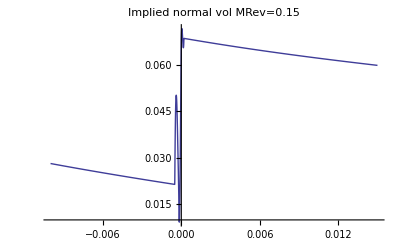
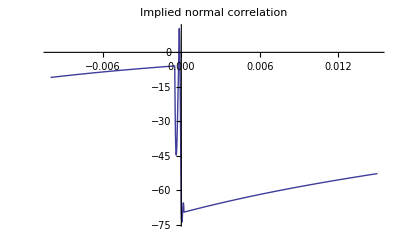

{34.523,Null}

```mathematica
Timing[Module[{S1,S2,M1=-0.35,M2=-0.35,ρs=0.1,ρsinf=0.1,ρm1=0.,ρm2=0.,ρ1=-0.45,ρ2=-0.45, Σ1,Σ2,θ1,θ2,τ=5,α1=1,a=1,M,Σinf,Σ,Q,βm,S,ρ,printflag={1},μ={0,0},inter1,inter2,inter3,smileLN,interLN,prices,tenor1="cms2",tenor2="cms10",K,β,limsup=1000,ρH1,νH2,ρH2,λH2,θH2,ν1,ν2,Lcoefs=LegendreCoeffs[40]},
Σ1=0.01;Σ2=0.01;θ1=3.Σ1;θ2=3.Σ2;
S1=MarketCMSForward[τ,tenor1][[1]];S2=MarketCMSForward[τ,tenor2][[1]];
M=({{M1, ρm1 √(M1 M2)}, {ρm2 √(M1 M2), M2}});Σinf=({{θ1, √(θ1 θ2) ρsinf}, {√(θ1 θ2) ρsinf, θ2}});Σ=({{Σ1, √(Σ1 Σ2) ρs}, {√(Σ1 Σ2) ρs, Σ2}});S={S1,S2};ρ={ρ1,ρ2};
Q=({{0.25, 0.01}, {0.01, 0.25}});
strikes={-0.01,-0.005,-0.002,-0.001,-0.0005,-0.0002,-0.0001,0,0.0001,0.0002,0.0005,0.001,0.002,0.005,0.0075,0.01,0.015};
prices=SmileBiHestonVanilla2[S,1,1,1,1,strikes,τ,Σ,M,Σinf,Q,ρ,μ,printflag];
smile=Table[{strikes[[i]],NormalImplicitVol[S1-S2,strikes[[i]],τ,prices[[i]]]},{i,1,Length[strikes]}];
inter1=Interpolation[smile];
smileMarket=Table[{strikes[[i]],MarketCMSSpreadOptionNormalVol[strikes[[i]],τ,tenor1,tenor2][[1]]},{i,1,Length[strikes]}];
interMarket1=Interpolation[smileMarket];
(* differrentes approx pour les vol normal des underlying *)
ν1=√(Q[[1,1]]^2+Q[[2,1]]^2);ν2=√(Q[[1,2]]^2+Q[[2,2]]^2);
ρH1=(Q[[1,1]]ρ1 +Q[[2,1]]ρ2)/(√(Q[[1,1]]^2+Q[[2,1]]^2));ρH2=(Q[[2,2]]ρ1 +Q[[1,2]]ρ2)/(√(Q[[2,2]]^2+Q[[1,2]]^2));
vol1=ImpVolHeston2[S1,S1,τ,Σ1,θ1,ρH1,-M1,ν1,Lcoefs];
vol2=ImpVolHeston2[S2,S2,τ,Σ2,θ2,ρH2,-M2,ν2,Lcoefs];
NormalVol1=vol1  S1;NormalVol1a=NormalImplicitVol[S1,S1,τ,BS[S1,S1,τ,vol1]];
NormalVol2=vol2 S2;NormalVol2a=NormalImplicitVol[S2,S2,τ,BS[S2,S2,τ,vol2]];
NormalVol1b=MarketCMSOptionVol[S1,τ,tenor1]  S1;
NormalVol2b=MarketCMSOptionVol[S2,τ,tenor2]  S2;
Print["ν1=",ν1," ν2=",ν2," ρH1=",ρH1," ρH2=",ρH2," vol1=",vol1," vol2=",vol2," NormalVol1=",NormalVol1," NormalVol2=",NormalVol2," NormalVol1a=",NormalVol1a," NormalVol2a=",NormalVol2a," NormalVol1b=",NormalVol1b," NormalVol2b=",NormalVol2b];

 smile=Table[{strikes[[i]],NormalImplicitCorrelation[NormalVol1 ,NormalVol2,inter1[strikes[[i]]]]},{i,1,Length[strikes]}];
inter10=Interpolation[smile];
 smileMarket=Table[{strikes[[i]],NormalImplicitCorrelation[NormalVol1 ,NormalVol2,interMarket1[strikes[[i]]]]},{i,1,Length[strikes]}];
interMarket10=Interpolation[smileMarket];
Print[{Plot[{inter1[x],interMarket1[x]},{x,strikes[[1]],Last[strikes]},PlotLabel->"Implied normal vol MRev=0.15",
PlotLegend->{"Biheston","Market"}],
Plot[{inter10[x],interMarket10[x]},{x,strikes[[1]],Last[strikes]},PlotLabel->"Implied normal correlation",
PlotLegend->{"Biheston","Market"}]}]]]
```

## Fit of the Initial Dynamics

```mathematica
le process sabr : dF/F=α/F^(1-β)Subscript[dW, 1]; dα=ν α  (ρ Subscript[dW, 1]+√(1-ρ^2))Subscript[dW, 2]
```

```mathematica
Var[Subscript[Y, 1]]=(α/F^(1-β))^2==Subscript[Σ, 11]
```

```mathematica
d[Subscript[Σ, 11]]=(2α dα)/F^(2-2β)+α^2(2β-2)F^(2β-3)dF=2α F^(2β-2)ν α  (ρ Subscript[dW, 1]+√(1-ρ^2))Subscript[dW, 2]+α^2(2β-2)F^(2β-3)α F^β Subscript[dW, 1]=
(2 α^2 F^(2β-2)ν  ρ +α^3(2β-2)F^(3β-3) )Subscript[dW, 1]+2 α^2 F^(2β-2)ν   √(1-ρ^2)Subscript[dW, 2]
```

```mathematica
so Var[Subscript[Σ, 11]]=(2 α^2 F^(2β-2)ν  ρ +α^3(2β-2)F^(3β-3) )^2+(2 α^2 F^(2β-2)ν   √(1-ρ^2))^2
```

```mathematica
le process de wishart :
```

```mathematica
Var[Subscript[Y, 1]]=Subscript[Σ, 11]
```

```mathematica
Var[Subscript[Σ, 11]]=4 Subscript[Σ, 11](Subscript[Q, 11]^2+Subscript[Q, 12]^2)
```

```mathematica
Covar[Subscript[Y, i],Subscript[Σ, 11]]=2 Subscript[Σ, 1i](Subscript[Q, 11] Subscript[ρ, 1]+Subscript[Q, 21] Subscript[ρ, 2])
```

Vect[(dS_(i,t))/(S_(i,t))]=√Σ_t dZ_t

dΣ_t=(M (Σ_t-Σ_∞)+ (Σ_t-Σ_∞)M^*)dt+√Σ_t dW_t Q +Q^*dW_t^*(√Σ_t)^*

```mathematica
Table[cms30[[i,j]],{i,1,Length[cms30]},{j,1,10}] // MatrixForm;
```

Nb1=62 Nb1n=30 Nb2=77

S=0.0481839
0.0481839 Σ=(0.015 | 0.00979796
0.00979796 | 0.01)M=(-0.15 | 0.
0. | -0.15) Σinf=(0.015 | 0.00979796
0.00979796 | 0.01) Q=(0.00948683 | 0.00619677
0. | 0.00464758) ρ=-0.45
-0.45 Imaginary Shifts=2
1.1

{NbLegCoef1,NbLegCoef1n,period1,period1n,ϵ1,imax}={62,30,14.52,12.,0.00001,10}

{NbLegCoef2,period2,period2n,ϵ2}={77,16.,1.6,0.00001}

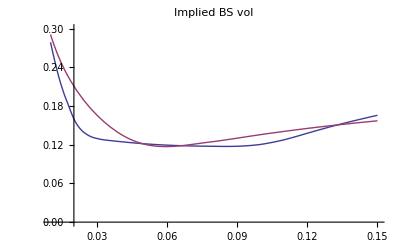
{24.328,-Graphics-}

```mathematica
Timing[Module[{S1,S2,M1=-0.15,M2=-0.15,ρs=0.8,ρsinf=0.8,ρm1=0.,ρm2=0.,ρ1=-0.45,ρ2=-0.45, Σ1,Σ2,θ1,θ2,β=5,τ=5,M,Σinf,Σ,Q,βm,S,ρ,printflag={1},μ={0,0},inter1,inter2,inter3,smileLN,interLN,prices,tenor="cms5",K,α1,a},Σ1=0.015;Σ2=0.01;θ1=Σ1;θ2=Σ2;α1=1;a=1;
S1=MarketCMSForward[τ,tenor][[1]];S2=S1;
M=({{M1, ρm1 √(M1 M2)}, {ρm2 √(M1 M2), M2}});Σinf=({{θ1, √(θ1 θ2) ρsinf}, {√(θ1 θ2) ρsinf, θ2}});Σ=({{Σ1, √(Σ1 Σ2) ρs}, {√(Σ1 Σ2) ρs, Σ2}});S={S1,S2};ρ={ρ1,ρ2};
strikes={0.01,0.0125,0.015,0.0175,0.02,0.025,0.03,0.035,0.04,0.045,0.048,0.05,0.055,0.06,0.08,0.1,0.11,0.12,0.13,0.14,0.15};
Q=CholeskyDecomposition[-((M.Σinf+Σinf. Transpose[M])/2)]/β;
Coef1=LegendreCoeffs[80];Coef2=LegendreCoeffs[30];
LegendreCoef1=Coef1;LegendreCoef1n=Coef2;period1=6;period1n=3;ϵ1=0.000001;LegendreCoef2=Coef1;period2=8;period2n=4;ϵ2=0.000001;imax=10;λ1=2;λ2=1.2;

prices=SmileBiHestonUnderlying1Vanilla[S,α1,a,strikes,τ,Σ,M,Σinf,β,ρ,μ,printflag];
smile=Table[{strikes[[i]],ImpVolBS[S1,strikes[[i]],τ,prices[[i]]]},{i,1,Length[strikes]}];
smileMarket=Table[{strikes[[i]],MarketCMSOptionVol[strikes[[i]],τ,tenor][[1]]},{i,1,Length[strikes]}];
inter=Interpolation[smile];
interMarket=Interpolation[smileMarket];
Plot[{inter[x],interMarket[x]},{x,strikes[[1]],Last[strikes]},PlotLabel->"Implied BS vol",
PlotLegend->{"BiHestonUnderlying1","Market"},LegendPosition->{1,0},PlotRange->{0,0.3}]]
]
```

```mathematica
Manipulate
```

```mathematica
Manipulate[Plot[Sin[a x+b],{x,0,6}],{{a,2,"Multiplier"},1,4},{{b,0,"Phase Parameter"},0,10}]
```

```mathematica
Manipulate[Module[{S1,S2,M1=-0.15,M2=-0.15,ρs=0.8,ρsinf=0.8,ρm1=0.,ρm2=0.,ρ1=-0.15,ρ2=-0.15, Σ1,Σ2,θ1,θ2,τ=5,α1=1,a=1,M,Σinf,Σ,Q,βm,S,ρ,printflag=0,μ={0,0},inter1,inter2,inter3,smileLN,interLN,prices,tenor="cms5",K},
Σ1=0.015;Σ2=0.01;θ1=1.Σ1;θ2=Σ2;
S1=MarketCMSForward[τ,tenor][[1]];S2=S1;
M=({{M1, ρm1 √(M1 M2)}, {ρm2 √(M1 M2), M2}});Σinf=({{θ1, √(θ1 θ2) ρsinf}, {√(θ1 θ2) ρsinf, θ2}});Σ=({{Σ1, √(Σ1 Σ2) ρs}, {√(Σ1 Σ2) ρs, Σ2}});S={S1,S2};ρ={ρ1,ρ2};
strikes={0.01,0.0125,0.015,0.0175,0.02,0.021,0.022,0.023,0.024,0.025,0.026,0.027,0.028,0.029,0.03,0.031,0.032,0.033,0.034,0.035,0.036,0.037,0.038,0.039,0.04,0.045,0.048,0.05,0.055,0.06,0.065,0.07,0.075,0.08,0.085,0.09,0.095,0.1,0.11,0.12};
Q=CholeskyDecomposition[-((M.Σinf+Σinf. Transpose[M])/2)]/β;
Coef1=LegendreCoeffs[20];Coef2=LegendreCoeffs[10];
LegendreCoef1=Coef1;LegendreCoef1n=Coef2;period1=10;period1n=5;ϵ1=0.000001;LegendreCoef2=Coef1;period2=12;period2n=1.6;ϵ2=0.000001;imax=3;λ1=2;λ2=1.2;
(* prices=SmileBiHestonUnderlying1Vanilla[S,α1,a,strikes,τ,Σ,M,Σinf,β,ρ,μ,printflag];*)
prices=SmileBiHestonUnderlying1VanillaAux[S,α1,a,strikes,τ,Σ,M,Σinf,Q,ρ,μ,β,λ1,λ2,{LegendreCoef1,LegendreCoef1n,period1,period1n,ϵ1,imax},{LegendreCoef2,period2,period2n,ϵ2},printflag];
smile=Table[{strikes[[i]],ImpVolBS[S1,strikes[[i]],τ,prices[[i]]]},{i,1,Length[strikes]}];
smileMarket=Table[{strikes[[i]],MarketCMSOptionVol[strikes[[i]],τ,tenor][[1]]},{i,1,Length[strikes]}];
inter=Interpolation[smile];
interMarket=Interpolation[smileMarket];
Plot[{inter[x],interMarket[x]},{x,strikes[[1]],Last[strikes]},PlotLabel->"Implied BS vol",
PlotLegend->{"BiHestonUnderlying1","Market"},LegendPosition->{1,0},PlotRange->{0,0.3}]],{{β,2.5,"Multiplier"},2,7}]
```

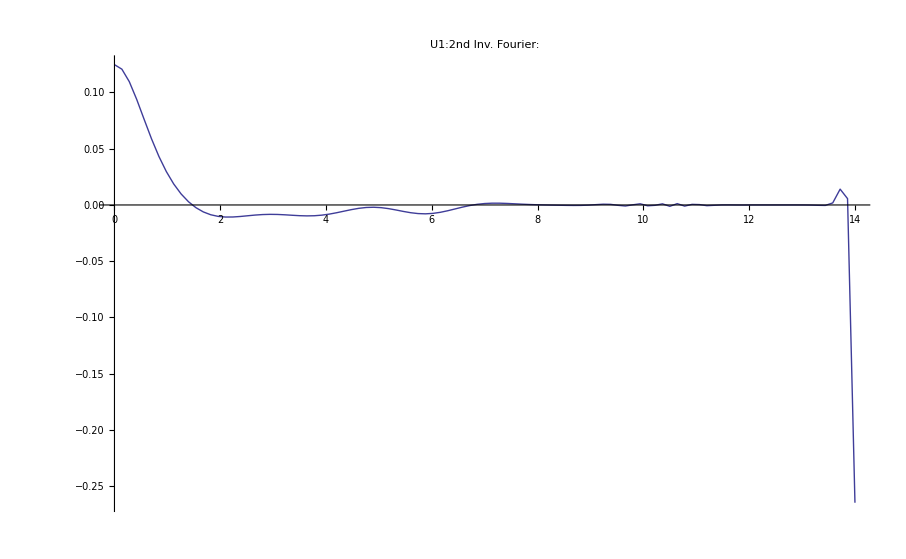
{15.547,-Graphics-}

```mathematica
Timing[Module[{S1,S2,M1=-0.35,M2=-0.35,ρs=0.5,ρsinf=0.5,ρm1=0.,ρm2=0.,ρ1=-0.45,ρ2=-0.45, Σ1,Σ2,θ1,θ2,τ=5,α1=1,a=1,M,Σinf,Σ,Q,βm,S,ρ,printflag={1},μ={0,0},inter1,inter2,inter3,smileLN,interLN,prices,tenor1="cms2",tenor2="cms10",K,β,limsup=1000,ρH1,νH2,ρH2,λH2,θH2,ν1,ν2,Lcoefs=LegendreCoeffs[40]},
Σ1=0.01;Σ2=0.01;θ1=3.Σ1;θ2=3.Σ2;
S1=MarketCMSForward[τ,tenor1][[1]];S2=MarketCMSForward[τ,tenor2][[1]];
M=({{M1, ρm1 √(M1 M2)}, {ρm2 √(M1 M2), M2}});Σinf=({{θ1, √(θ1 θ2) ρsinf}, {√(θ1 θ2) ρsinf, θ2}});Σ=({{Σ1, √(Σ1 Σ2) ρs}, {√(Σ1 Σ2) ρs, Σ2}});S={S1,S2};ρ={ρ1,ρ2};
Q=({{0.25, 0.01}, {0.01, 0.25}});
Test2BiHestonVanilla2[S,1,1,1,1,-0.01,τ,Σ,M,Σinf,Q,ρ,μ,1.1,1.01,{LegendreCoeffs[30],LegendreCoeffs[15],8,5,0.0000001,20},14]]]
```

```mathematica
Timing[Module[{S1,S2,M1=-0.35,M2=-0.35,ρs=0.5,ρsinf=0.5,ρm1=0.,ρm2=0.,ρ1=-0.45,ρ2=-0.45, Σ1,Σ2,θ1,θ2,τ=5,α1=1,a=1,M,Σinf,Σ,Q,βm,S,ρ,printflag={1},μ={0,0},inter1,inter2,inter3,smileLN,interLN,prices,tenor1="cms2",tenor2="cms10",K,β,limsup=1000,ρH1,νH2,ρH2,λH2,θH2,ν1,ν2,Lcoefs=LegendreCoeffs[40]},
Σ1=0.01;Σ2=0.01;θ1=3.Σ1;θ2=3.Σ2;
S1=MarketCMSForward[τ,tenor1][[1]];S2=MarketCMSForward[τ,tenor2][[1]];
M=({{M1, ρm1 √(M1 M2)}, {ρm2 √(M1 M2), M2}});Σinf=({{θ1, √(θ1 θ2) ρsinf}, {√(θ1 θ2) ρsinf, θ2}});Σ=({{Σ1, √(Σ1 Σ2) ρs}, {√(Σ1 Σ2) ρs, Σ2}});S={S1,S2};ρ={ρ1,ρ2};
Q=({{0.25, 0.01}, {0.01, 0.25}});βm=-((M.Σinf+Σinf.Transpose[M])/2).Inverse[(Transpose[Q].Q)];
Plot[SmileSymetrizedBiHestonVanillaIntegrand2[{Log[S[[1]]],Log[S[[2]]]},1,1,1,1,{S1},τ,Σ,M,Q,ρ,μ,βm,1.1,1.01,14,ω2][[1]],{ω2,14.38 ,14.40}]]]
```

{9.344,-Graphics-}

```mathematica
Explosion typique
```

```mathematica
Timing[Module[{S1,S2,M1=-0.35,M2=-0.35,ρs=0.5,ρsinf=0.5,ρm1=0.,ρm2=0.,ρ1=-0.45,ρ2=-0.45, Σ1,Σ2,θ1,θ2,τ=5,α1=1,a=1,M,Σinf,Σ,Q,βm,S,ρ,printflag={1},μ={0,0},inter1,inter2,inter3,smileLN,interLN,prices,tenor1="cms2",tenor2="cms10",K,β,limsup=1000,ρH1,νH2,ρH2,λH2,θH2,ν1,ν2,Lcoefs=LegendreCoeffs[40]},
Σ1=0.01;Σ2=0.01;θ1=3.Σ1;θ2=3.Σ2;
S1=MarketCMSForward[τ,tenor1][[1]];S2=MarketCMSForward[τ,tenor2][[1]];
M=({{M1, ρm1 √(M1 M2)}, {ρm2 √(M1 M2), M2}});Σinf=({{θ1, √(θ1 θ2) ρsinf}, {√(θ1 θ2) ρsinf, θ2}});Σ=({{Σ1, √(Σ1 Σ2) ρs}, {√(Σ1 Σ2) ρs, Σ2}});S={S1,S2};ρ={ρ1,ρ2};
Q=({{0.25, 0.01}, {0.01, 0.25}});βm=-((M.Σinf+Σinf.Transpose[M])/2).Inverse[(Transpose[Q].Q)];
SmileSymetrizedBiHestonVanillaIntegrand2[{Log[S[[1]]],Log[S[[2]]]},1,1,1,1,{S1},τ,Σ,M,Q,ρ,μ,βm,1.1,1.01,14,14.398]]]
```

{0.015,{1.04261×10^302}}

```mathematica
Module[{S1,S2,M1=-0.35,M2=-0.35,ρs=0.5,ρsinf=0.5,ρm1=0.,ρm2=0.,ρ1=-0.45,ρ2=-0.45, Σ1,Σ2,θ1,θ2,τ=5,α1=1,a=1,M,Σinf,Σ,Q,βm,S,ρ,printflag={1},μ={0,0},inter1,inter2,inter3,smileLN,interLN,prices,tenor1="cms2",tenor2="cms10",K,β,limsup=1000,ρH1,νH2,ρH2,λH2,θH2,ν1,ν2,Lcoefs=LegendreCoeffs[40]},
Σ1=0.01;Σ2=0.01;θ1=3.Σ1;θ2=3.Σ2;
S1=MarketCMSForward[τ,tenor1][[1]];S2=MarketCMSForward[τ,tenor2][[1]];
M=({{M1, ρm1 √(M1 M2)}, {ρm2 √(M1 M2), M2}});Σinf=({{θ1, √(θ1 θ2) ρsinf}, {√(θ1 θ2) ρsinf, θ2}});Σ=({{Σ1, √(Σ1 Σ2) ρs}, {√(Σ1 Σ2) ρs, Σ2}});S={S1,S2};ρ={ρ1,ρ2};
Q=({{0.25, 0.01}, {0.01, 0.25}});βm=-((M.Σinf+Σinf.Transpose[M])/2).Inverse[(Transpose[Q].Q)];
SmileSymetrizedBiHestonVanillaIntegrand2[{Log[S[[1]]],Log[S[[2]]]},1,1,1,1,{S1},τ,Σ,M,Q,ρ,μ,βm,1.1,1.01,14,14.398]]
```

EXPH=(5693.08-6884.29 ⅈ | 5778.7-7126.47 ⅈ | -101.95+24.6502 ⅈ | -103.022+27.6945 ⅈ
5947.53-7001.75 ⅈ | 6041.5-7257.19 ⅈ | -105.063+23.8537 ⅈ | -106.491+27.2394 ⅈ
-620538.+75063.2 ⅈ | -636829.+83320.6 ⅈ | 6355.28+3660.21 ⅈ | 6570.44+3559.32 ⅈ
-636829.+83320.6 ⅈ | -653421.+92042.5 ⅈ | 6566.76+3698.81 ⅈ | 6785.94+3588.81 ⅈ) δ=-37051.7-61256.3 ⅈ LogA11={{5.47235-1.06926 ⅈ,4.22668+0.130713 ⅈ},{4.22805+0.227444 ⅈ,5.70637-1.04553 ⅈ}}

EXPH=(50587.9+31210.8 ⅈ | -49335.8-36056.7 ⅈ | -792.232-9.62675 ⅈ | 312.592+739.823 ⅈ
-45566.7+39377.4 ⅈ | 49872.3-36694.5 ⅈ | 250.529-762.561 ⅈ | -810.226+76.7806 ⅈ
-3.68712×10^6+476522. ⅈ | 3.81736×10^6-191888. ⅈ | 38864.9-30738.9 ⅈ | -44334.6-23626.2 ⅈ
3.81736×10^6-191888. ⅈ | -3.92794×10^6-110316. ⅈ | -42305.5+28379.8 ⅈ | 43540.+27780.5 ⅈ) δ=310303.-12500.3 ⅈ LogA11={{6.19199+3.48482 ⅈ,-4.912-3.96437 ⅈ},{-4.89633+3.83746 ⅈ,6.45412-3.52509 ⅈ}}

EXPH=(889.193-8151.77 ⅈ | -354.286-8356.54 ⅈ | -72.6505+70.2175 ⅈ | -56.627+74.2457 ⅈ
63.3176-9331.69 ⅈ | -1366.97-9427.44 ⅈ | -74.0363+87.7745 ⅈ | -55.6857+90.7777 ⅈ
-433636.+423470. ⅈ | -372529.+493721. ⅈ | 7438.84-594.165 ⅈ | 6727.84-1577.2 ⅈ
-372529.+493721. ⅈ | -300033.+555277. ⅈ | 7414.28-1738.91 ⅈ | 6544.74-2625.38 ⅈ) δ=-62735.2-16574.9 ⅈ LogA11={{5.23795-0.894869 ⅈ,4.02684-0.209526 ⅈ},{4.49887-0.0127297 ⅈ,5.84246-1.98842 ⅈ}}

EXPH=(56094.-11391.6 ⅈ | -57123.6+15334.8 ⅈ | -564.555+487.859 ⅈ | 710.909+280.095 ⅈ
-2545.08+58382.5 ⅈ | -1103.62-60378.2 ⅈ | -344.19-679.558 ⅈ | -452.91+635.301 ⅈ
-2.1115×10^6+2.78315×10^6 ⅈ | 1.99989×10^6-3.00551×10^6 ⅈ | 6205.41-45112.3 ⅈ | -43874.7+15822. ⅈ
1.99989×10^6-3.00551×10^6 ⅈ | -1.87056×10^6+3.22771×10^6 ⅈ | -3516.2+46925.4 ⅈ | 44241.2-19123.3 ⅈ) δ=186447.-235686. ⅈ LogA11={{6.46283+3.81672 ⅈ,-5.66989-3.5842 ⅈ},{-5.06365+4.27582 ⅈ,6.15043-4.71823 ⅈ}}

propagatorDroit=-0.00471543+0.0111007 ⅈ SympropagatorDroit=-1.36446×10^307+4.90056×10^307 ⅈ propagatorGauche=2.55514×10^-8-1.56957×10^-8 ⅈ SympropagatorGauche=-7.06008×10^-225+2.43617×10^-226 ⅈ

{1.04261×10^302}

```mathematica
BiHestonLaplaceQuickTransform2[{{M11_,M12_},{M21_,M22_}},{{Q11_,Q12_},{Q21_,Q22_}},{ρ1_,ρ2_},{μ1_,μ2_},{{Σ11_,Σ12_},{Σ21_,Σ22_}},{γ1_,γ2_},{{β11_,β12_},{β21_,β22_}},τ_]:=
Module[{EXPH=MatrixExp[τ{{1/2 (-M11-Q11 γ1 ρ1-Q21 γ1 ρ2),1/2 (-M12-Q11 γ2 ρ1-Q21 γ2 ρ2),1/2 (-Q11^2-Q21^2),1/2 (-Q11 Q12-Q21 Q22)},{1/2 (-M21-Q12 γ1 ρ1-Q22 γ1 ρ2),1/2 (-M22-Q12 γ2 ρ1-Q22 γ2 ρ2),1/2 (-Q11 Q12-Q21 Q22),1/2 (-Q12^2-Q22^2)},{-γ1/2+γ1^2/2+γ1 μ1,(γ1 γ2)/2,1/2 (M11+Q11 γ1 ρ1+Q21 γ1 ρ2),1/2 (M21+Q12 γ1 ρ1+Q22 γ1 ρ2)},{(γ1 γ2)/2,-γ2/2+γ2^2/2+γ2 μ2,1/2 (M12+Q11 γ2 ρ1+Q21 γ2 ρ2),1/2 (M22+Q12 γ2 ρ1+Q22 γ2 ρ2)}}],δ,LogA11},
δ=-EXPH[[1,2]] EXPH[[2,1]]+EXPH[[1,1]] EXPH[[2,2]];
LogA11=MatrixLog2[{{EXPH[[1,1]],EXPH[[1,2]]},{EXPH[[2,1]],EXPH[[2,2]]}}];
Print["EXPH=",EXPH // MatrixForm," δ=",δ," LogA11=",LogA11];
A={{EXPH[[2,2]] EXPH[[3,1]] -EXPH[[1,2]] EXPH[[4,1]] ,+EXPH[[2,2]] EXPH[[3,2]]-EXPH[[1,2]] EXPH[[4,2]]},
{+EXPH[[1,1]] EXPH[[4,1]]-EXPH[[2,1]] EXPH[[3,1]],+EXPH[[1,1]] EXPH[[4,2]]-EXPH[[2,1]] EXPH[[3,2]] }}/δ;
Print["A=",A];
Exp[1/δ((EXPH[[2,2]] EXPH[[3,1]] -EXPH[[1,2]] EXPH[[4,1]] )Σ11+(EXPH[[2,2]] EXPH[[3,2]]-EXPH[[1,2]] EXPH[[4,2]]+EXPH[[1,1]] EXPH[[4,1]]-EXPH[[2,1]] EXPH[[3,1]]) Σ12+
 (EXPH[[1,1]] EXPH[[4,2]]-EXPH[[2,1]] EXPH[[3,2]]) Σ22)-2(β11 LogA11[[1,1]]+β12 LogA11[[1,2]]+β21 LogA11[[2,1]]+β22 LogA11[[2,2]]+1/2 (β11 (M11+Q11 γ1 ρ1+Q21 γ1 ρ2)+β21 (M21+Q12 γ1 ρ1+Q22 γ1 ρ2)+β12 (M12+Q11 γ2 ρ1+Q21 γ2 ρ2)+β22 (M22+Q12 γ2 ρ1+Q22 γ2 ρ2)) τ)]
]
```